# A mathematical model for universal semantics (Text mining in Dutch)

### Weinan E and Yajun Zhou

## Introduction

Accompanying the topic extraction and word translation sections in [1], this Mathematica Notebook file is optimized for v11.0, and it will also run on v10.3 and v10.4. Earlier versions of Mathematica do not contain certain text analysis functionalities required for this program.

Unless explicitly stated otherwise, all the routines (word clustering, word cloud plotting and question answering) below are specifically designed for the current work [1], instead of being imported elsewhere.

[1] W. E and Y. Zhou, “A mathematical model for universal semantics,” 2020, arXiv:1907.12293v6 [cs.CL].

## Preparations

Text corpora mentioned below need to be stored in the following directory (or anywhere else that you redesignate)

```mathematica
SetDirectory["D:\\Documents"]
```

D:\Documents

This Mathematica Notebook file MUST BE executed AFTER all the cells in English.nb are evaluated.

### Pride and Prejudice

The full text for a Dutch translation of Jane Austen’s Pride and Prejudice is commercially available from 
https://www.amazon.de/Trots-vooroordeel-Dutch-Jane-Austen-ebook/dp/B00NY0LO1W/

After manual cleansing, we save the text as Trots en vooroordeel.txt,  which begins with

Hoofdstuk 1



Het is een waarheid die iedereen, waar ook ter wereld, zal onderschrijven: een ongehuwde man met een behoorlijk vermogen heeft behoefte aan een echtgenote.

Hoe weinig er ook bekend mag

and ends with

n. Zowel Darcy als Elizabeth waren zeer op hen gesteld en ze bleven beiden zeer dankbare gevoelens koesteren tegenover de mensen die hen, door met haar naar Derbyshire te reizen, hadden samengebracht.

Making sure that all the cells in English.nb have been evaluated, you are ready to execute all the cells in this file.

## Dutch (pre- and post-1946/1947 orthographies)

## Dutch stop words

Our list of stop words is essentially based on

snowball.tartarus.org/algorithms/dutch/stop.txt

plus the following words involved in archaic Dutch declensions and records of colloquial speech:

```mathematica
{"des","der","'s","den","d'n","'n","ene","'ne","eens","'ns","ener","eens","enen","nen","deze","dezes","dezen","dezer","dien","diens","dier","'k"}
```

{des,der,'s,den,d'n,'n,ene,'ne,eens,'ns,ener,eens,enen,nen,deze,dezes,dezen,dezer,dien,diens,dier,'k}

```mathematica
DutchStopWords={"aan","al","alles","als","altijd","andere","ben","bij","daar","dan","dat","de","den","der","des","deze","dezen","dezer","dezes","die","dien","diens","dier","dit","d'n","doch","doen","door","dus","een","eens","en","ene","enen","ener","er","ge","geen","geweest","haar","had","heb","hebben","heeft","hem","het","hier","hij","hoe","hun","iemand","iets","ik","in","is","ja","je","'k","kan","kon","kunnen","maar","me","meer","men","met","mij","mijn","moet","'n","na","naar","'ne","nen","niet","niets","nog","'ns","nu","of","om","omdat","onder","ons","ook","op","over","reeds","'s","te","tegen","toch","toen","tot","u","uit","uw","van","veel","voor","want","waren","was","wat","werd","wezen","wie","wil","worden","wordt","zal","ze","zelf","zich","zij","zijn","zo","zonder","zou"}∪{"wellicht","misschien","hoewel","eenieder","iedereen","elk","elke","alle","altijd","nooit","enig","enige","weinig","weinige","minder","minst","minste","vele","meest","meeste","bent","we","jullie","waar","weer","zeer","noch","ooit","niemand","wij","hoeveel","k","n","t","gij","jij","jou","hen","jouw","mijne","jouwe","uwe","zijne","hare","onze","hunne","mijner","jouwer","uwer","zijner","onzer","hunner","ieder","iedere","heel","hele","wel","beide","beiden","hebt","hebbe","hebbend","hadt","hadden","gehad","zijt","wees","weest","zijnd","waart","even","ten","ter"}∪{"moeten","moet","moete","moetend","moest","moesten","moeste","gemoeten"}∪{"mogen","mag","moogt","moge","mogend","mocht","mochte","mochten","gemogen"}∪{"kunnen","kunt","kunnend","kon","kondt","konden","gekund"}∪{"nee","neen","af","allen"}∪{"tot","toe","ertoe","hiertoe","daartoe","waartoe","zoveel"}∪{"anders","andere","ander","allemaal","helemaal"}∪{"doen","doe","doet","doend","deed","deedt","deden","gedaan"}∪{"nu","nou"}∪{"waarom","sint","mindere","minderen","eenmaal"}∪{"met","mee","ermee","hiermee","daarmee","waarmee"}∪{"daarom","daarna","daarop","zolang","zoals","bijna","evenmin","eventjes","minstens","vroeger","later","allebei"}∪{"dikwijls","meteen","onmiddellijk","soms","straks","vaak","achter","achteruit","boven","ergens","heen","naartoe","nergens","terug","vandaan","vooruit","hoelang","vanwaar","wanneer","waarheen","waarvandaan","bovendien","daarnaast","daardoor","desondanks","echter","eventueel","evenwel","hiervoor","tevens","vooral","nergens","ergens","daarvan","hiervan","ervan","waarvandaan","allang","echt","eigenlijk","erg","eveneens","evengoed","evenzeer","intussen","nauwelijks","net","niettemin","tenminste","tenslotte","zelden","zojuist"}∪{"waarop"}∪{"zal","zou","zoude","zouden","zoudt","zulle","zullen","zullend","zult"}∪{"enkel","enkele","enkels","genoeg","luttel","luttele","menig","menige","sommige","sommigen"}∪{"welk","welke","hetwelk","hetgeen"}∪{"vake","vaaks","vaker","vaakst"}∪{"dergelijk","dergelijke","dergelijks"}∪{"elkaar","elkaars","trouwens","zulk","zulke","zulks","sindsdien","werden","werdt","word","wordt","wordend","geworden","mijzelf","jijzelf","uzelf","zich","zichzelf","onszelf","jezelf","hetzelfde","dezelfde"}∪{"erop","hierop","daarop","waarop","eronder","hieronder","daaronder","waaronder","erom","hierom","daarom","waarom","erin","hierin","daarin","waarin"}∪{"behalve","elders","degene","degenen","diegene","diegenen","hetgeen","vanaf","naartoe","datgene","datgenen"}∪{"beneden","naast","ernaast","hiernaast","daarnaast","waarnaast","per"};
```

To accommodate to pre-1946 (Flanders)/pre-1947 (Netherlands) Dutch written standard, which employed a sophisticated case system as in modern German (see https://en.wikipedia.org/wiki/Archaic_Dutch_declension), we need to add inflected forms of the definite and indefinite articles, as well as those of the demonstratives to the list of stop words. It should be noted that archaic Dutch declensions still survive in some stock phrases in modern Dutch, such as the genitive construction in het Koninkrijk der Nederlanden (“the Kingdom of Netherlands”).

## Dutch sample words

The following inflected forms of nouns and adjectives include archaic declensions found in the paradigms on the following web-page: en.wikipedia.org/wiki/Archaic_Dutch_declension

We have also included some diminuitive forms of nouns, as well as several compounds.

```mathematica
goodDutch={"best","beste","beter","betere","beters","goed","goede","goeden","goeder","goeds"};manDutch={"man","mans","manne","mannen"};womanDutch={"vrouw","vrouwe","vrouwen"};smallDutch={"klein","kleine","kleinen","kleiner","kleinere","kleiners","kleins","kleinst","kleinste"};deedDutch={"daad","daden"};moonDutch={"maan","manen","maantje"};eggDutch={"ei","eieren","eitje","eitjes"};eggyolkDutch={"eidooier","eidooiers","eidooiertje","eierdooier","eierdooiers","eierdooiertje"};yolkDutch={"dooier","dooiers","dooiertje"};eggwhiteDutch={"eiwit","eiwitten","eiwittje"};whiteDutch={"wit","wits","witst","witste","witte","witter","wittere","witters"};
```

```mathematica
DutchSampleNounsAdjectives=goodDutch∪manDutch∪womanDutch∪smallDutch∪deedDutch∪moonDutch∪eggDutch∪eggyolkDutch∪yolkDutch∪eggwhiteDutch∪whiteDutch;
```

Regular verbs, also known as weak verbs, form an overwhelming majority in the inventory of Dutch verbs. We will test the clustering algorithm on four regular verbs.

```mathematica
workDutch={"gewerkt","werk","werke","werken","werkend","werkt","werkte","werkten"};learnDutch={"geleerd","leer","leerde","leerden","leert","lere","leren","lerend"};rageDutch={"geraasd","raas","raasde","raasden","raast","raze","razen","razend"};dumpDutch={"gelost","los","losse","lossen","lossend","lost","loste","losten"};
```

```mathematica
DutchSampleRegularVerbs=workDutch∪learnDutch∪rageDutch∪dumpDutch;
```

```mathematica
DutchSimpleWords=DutchSampleNounsAdjectives∪DutchSampleRegularVerbs;
```

However, like English, Dutch has about 200 irregular verbs in common use. Most of these irregular verbs exhibit vowel alternations in various patterns. We pick representative verbs from the seven classes of Dutch strong conjugation (https://en.wiktionary.org/wiki/Category:Dutch_strong_verbs) in the list below.

```mathematica
bakeDutch={"bak","bakke","bakken","bakkend","bakt","bakte","bakten","gebakken"};expelDutch={"ban","bande","banden","banne","bannen","bannend","bant","gebannen"};askDutch={"gevraagd","vraag","vraagd","vraagde","vraagden","vraagt","vrage","vragen","vragend","vroeg","vroege","vroegen","vroegt"};bringDutch={"bracht","brachte","brachten","breng","brenge","brengen","brengend","brengt","gebracht"};thinkDutch={"dacht","dachte","dachten","denk","denke","denken","denkend","denkt","gedacht"};buyDutch={"gekocht","kocht","kochte","kochten","koop","koopt","kope","kopen","kopend"};seekDutch={"gezocht","zocht","zochte","zochten","zoek","zoeke","zoeken","zoekend","zoekt"};biteDutch={"beet","bete","beten","bijt","bijte","bijten","bijtend","gebeten"};appearDutch={"bleek","bleekt","bleke","bleken","blijk","blijke","blijken","blijkend","blijkt","gebleken"};deceiveDutch={"bedrieg","bedriege","bedriegen","bedriegend","bedriegt","bedroge","bedrogen","bedroog","bedroogt"};bidDutch={"bied","biede","bieden","biedend","biedt","bode","boden","bood","boodt","geboden"};bendDutch={"boge","bogen","boog","boogt","buig","buige","buigen","buigend","buigt","gebogen"};dripDutch={"droop","droopt","drope","dropen","druip","druipe","druipen","druipend","druipt","gedropen"};beginDutch={"begin","beginne","beginnen","beginnend","begint","begon","begonne","begonnen","begont"};tieDutch={"bind","binde","binden","bindend","bindt","bond","bonde","bonden","bondt","gebonden"};applyDutch={"gegolden","geld","gelde","gelden","geldend","geldt","gold","golde","golden","goldt"};scoldDutch={"gescholden","scheld","schelde","schelden","scheldend","scheldt","schold","scholde","scholden","scholdt"};weighDutch={"gewogen","weeg","weegt","wege","wegen","wegend","woge","wogen","woog","woogt"};blowDutch={"blaas","blaast","blaze","blazen","blazend","blies","bliest","blieze","bliezen","geblazen"};carryDutch={"draag","draagt","drage","dragen","dragend","droeg","droege","droegen","droegt","gedragen"};lieDutch={"gelegen","laagt","lag","lage","lagen","lig","ligge","liggen","liggend","ligt"};sitDutch={"gezeten","zat","zate","zaten","zit","zitte","zitten","zittend"};spoilDutch={"bederf","bederft","bederve","bederven","bedervend","bedierf","bedierft","bedorve","bedorven"};helpDutch={"geholpen","help","helpe","helpen","helpend","helpt","hielp","hielpe","hielpen","hielpt"};breakDutch={"braakt","brak","brake","braken","breek","breekt","breke","breken","brekend","gebroken"};takeDutch={"genomen","naamt","nam","name","namen","neem","neemt","neme","nemen","nemend"};heaveDutch={"geheven","hef","heffe","heffen","heffend","heft","hief","hieft","hieve","hieven"};createDutch={"geschapen","schep","scheppe","scheppen","scheppend","schept","schiep","schiepe","schiepen","schiept"};
```

```mathematica
DutchSampleIrregularVerbs=bakeDutch∪expelDutch∪askDutch∪bringDutch∪thinkDutch∪buyDutch∪seekDutch∪biteDutch∪appearDutch∪deceiveDutch∪bidDutch∪bendDutch∪dripDutch∪beginDutch∪tieDutch∪applyDutch∪scoldDutch∪weighDutch∪blowDutch∪carryDutch∪lieDutch∪lieDutch∪sitDutch∪spoilDutch∪helpDutch∪breakDutch∪takeDutch∪heaveDutch∪createDutch;
```

NOTES:

The 1946/1947 orthography reform changed the endings of certain words: bosch (“forest”), mensch (“human”) and visch (“fish”, singular noun) are now spelt bos, mens and vis, respectively. (See §2.1 of Bruce C. Donaldson’s grammar book.) Meanwhile, the spellings of mathematisch (“mathematical”) and typisch (“typical”) are not affected, despite having the same silent -ch ending. So long as a document consistently employs an orthographical standard, we do not need to worry about these changes in our clustering algorithm, and we will not forcibly change all word final -sch to s.

## Approximate clustering of Dutch words

The clustering routine is described below.

### Effective spelling and essential root

```mathematica
DutchEffVowels="a"|"e"|"i"|"o"|"u"|"y"|"ê"|"î"|"ô"|"û"|"ü"|"A"|"E"|"O"|"U";
```

```mathematica
DutchEffSpell[w_]:=StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[ToLowerCase[w],{"gardiner":>"φarδiner","aanwezig"~~___:>"πρϵsenτ","afwezig"~~___:>"αβσenτ",WordBoundary~~"genegen":>"nijgen",WordBoundary~~"schoonh":>"mooih","meester":>"μeeστer","gezag":>"αuτρg","gezicht":>"ϕaσt",WordBoundary~~"ma"~~"'s"|"’s"|"atje"~~""|"s"~~WordBoundary:>"moeder",WordBoundary~~"mam"~~"me"~~"n"|"tje"~~""|"s"~~WordBoundary:>"moeder",WordBoundary~~"pappa"~~""|"a":>"vader",WordBoundary~~"ma"~~""|"m"~~"ma"~~""|"a":>"moeder",
"mooie"~~___~~WordBoundary:>"mooi","ellend":>"μiσρβd",WordBoundary~~"ped":>"peδ","wonder":>"wonδer",WordBoundary~~""|"ge"~~"rend"~~""|"e"|"en"~~WordBoundary:>"rennen","schok":>"σχok",WordBoundary~~"kilo":>"κιλo",WordBoundary~~"o"~~"or"|"re":>"ϵaρ",WordBoundary~~"triest":>"τρieστt",WordBoundary~~"kind":>"κiλδd",WordBoundary~~"compl":>"κμλ",WordBoundary~~"manier":>"μaνieρr",WordBoundary~~"bezet":>"βζet",WordBoundary~~"eerb":>"ehrβ",WordBoundary~~"jone":>"γoνϵ","tafel":>"τaβλl","diner":>"δineρ",WordBoundary~~"forst":>"ϕorστ",WordBoundary~~"negen":>"9e","plant":>"planτ",WordBoundary~~"oom"~~""|"s"~~WordBoundary:>"oνκλ",WordBoundary~~"gelo"~~(s:("of"|"v")):>"βλlo"<>s,WordBoundary~~"vier":>"4er",WordBoundary~~"eerder":>"vroeg",WordBoundary~~"langza":>"σλoωza",WordBoundary~~"jane"~~WordBoundary:>"γιoνα","wit":>"ωiτt",WordBoundary~~""|"ge"~~"zegen":>"βλeσn"}],{"geget":>"et","voeld":>"fôl","isme"|"ist"~~""|"en"|"tje"~~""|"s"~~WordBoundary:>"e",WordBoundary~~"moe"~~""|"ie":>"mμmoe","leraar":>"leren","koning":>"κoning","d"~~"je"~~""|"s"~~WordBoundary:>"d",WordBoundary~~"janu":>"jnu",WordBoundary~~"geëe":>"geE","bruik":>"βruik","placht":>"pleeg","zicht":>"zien","lof":>"λof","lov":>"λov","loof":>"λoof",WordBoundary~~"zom":>"ζom","tien":>"tzien","tuin":>"τuin",""|"ge"~~"hoor":>"χoor","hor":>"χor","los":>"xlos","la"~~"s"|"ast"|"zen"|"ze"~~WordBoundary:>"lezen","la"~~"g"|"agt"|"gen"|"ge"~~WordBoundary:>"liggen","zat"~~""|"e"|"en"~~WordBoundary:>"zitten",WordBoundary~~"su":>"xsu",WordBoundary~~"ziek":>"xziek",WordBoundary~~(x0:"do"~~"od"|"d"):>"t"<>x0,WordBoundary~~"docht":>"dtocht",WordBoundary~~(x:"bra"~~"af"|"v"):>"p"<>x,WordBoundary
~~"zoon":>"xxzoon",WordBoundary~~"lie"~~(c:"f"|"v")~~""|"st":>"xlî"<>c,WordBoundary~~"georg":>"jgeorg","uk"~~WordBoundary:>"ukk",WordBoundary~~"best"~~""|"e"~~WordBoundary:>"gôd",WordBoundary~~"beter"~~""|"e"|"s"~~WordBoundary:>"gôd",WordBoundary~~"sir"~~WordBoundary:>"ssir","ga"~~""|"at"|"an"|"and"~~WordBoundary:>"ging","zag"~~""|"e"|"en"~~WordBoundary:>"zîn","zaagt"~~WordBoundary:>"zîn",""|"ge"~~"zegd":>"zeg","zei"~~""|"dt"|"den"|"de"~~WordBoundary:>"zeg","sta"~~""|"at"|"an"|"and"~~WordBoundary:>"stond","ga"~~"f"|"aft"|"ven"|"ve"~~WordBoundary:>"geven","gezond":>"jgezond","kwa"~~"m"|"men"|"me"|"amt"~~WordBoundary:>"komen","kom"~~""|"t"~~WordBoundary:>"komen","wist"~~""|"e"|"en"~~WordBoundary:>"weten","ä":>"a","ë":>"e","ï":>"i","ö":>"o","ü":>"u","á":>"a","é":>"e","í":>"i","ó":>"o","ú":>"u","è":>"e","oe":>"ô","ou":>"û","ij"|"ĳ":>"y"}],{"list":>"λist","ei":> "ê","ui":>"ü"}],{WordBoundary~~"aan"~~""|"ge"~~"n":>"n",WordBoundary~~"om"~~""|"ge"~~"m":>"m",WordBoundary~~"op"~~""|"ge"~~"p":>"p",WordBoundary~~"door"~~""|"ge"~~"r":>"r",WordBoundary~~"dwars"~~""|"ge"~~"s":>"s",WordBoundary~~"voort"~~""|"ge"~~"t":>"t",WordBoundary~~"weg"~~""|"ge"~~"g":>"g","ie":>"î"}],{"end"~~WordBoundary:>"e",(c:Except[DutchEffVowels])~~"s"~~WordBoundary:>c,(c0:LetterCharacter)~~"vaardig"|"ery"~~___:>c0,(c1:LetterCharacter)~~"vol"|"dom"~~("e"|"l"|"s"|"t"|"r")...:>c1}],{(c1:WordCharacter)~~"v":>c1<>"f",(c2:WordCharacter)~~"z":>c2<>"s",x_~~x_->ToUpperCase[x]}],"en"~~WordBoundary:>"e"],{(v:"a"|"e"|"o"|"u")~~(c:Except["a"|"e"|"i"|"o"|"u"|"y",CharacterRange["a","z"]])~~"e"~~WordBoundary:>ToUpperCase[v]<>c,(v:"a"|"e"|"i"|"o"|"u")~~(c:Except["A"|"E"|"I"|"O"|"U"|"Y",CharacterRange["A","Z"]])~~"e"~~WordBoundary:>v<>ToLowerCase[c]}],{"tje"~~""|"s"~~WordBoundary:>"","Tje"~~""|"s"~~WordBoundary:>"t",WordBoundary~~"vrE":>"βrE","An"~~""|"en"|"tje"~~""|"s"~~WordBoundary:>"a","îr"~~""|"s"|"es"|"tje"~~""|"s"~~WordBoundary:>"","lerares":>"lEr","sje"~~""|"s"~~WordBoundary:>"s","blîs":>"blEs"}]
```

```mathematica
DutchProtectedRange[word_]:=Max[Last[Last[Join[{{0,0}},StringPosition[word,WordBoundary~~(""|"a"|"e"|"i"|"u"|"ô"|"û"|"ü"|"A"|"E"|"O"|"U"|"her"|"be"|"ver"|"ge"|"mede"|"na"~~Except[DutchEffVowels]...~~Except["e",DutchEffVowels])|(Except[DutchEffVowels]..~~"e"|"E")~~Except["a"|"e"|"i"|"u"|"ê"|"î"|"ô"|"û"|"ü"|"A"|"E"|"O"|"U"|"r"]...]]]],Last[Last[Join[{{0,0}},StringPosition[word,"a"|"o"|"u"|"ô"|"û"|"A"|"O"|"U"]]]]]
```

```mathematica
DutchEssRootPreBlot[word_]:=(tag=word;hL=DutchProtectedRange[tag];StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringTake[tag,hL]<>StringReplace[StringReplace[StringDrop[tag,hL],{"s"|"Er"~~WordBoundary:>""}],{"e"~~(("d"|"e"|"m"|"n"|"r"|"st"|"t")...)~~WordBoundary:>""}],WordBoundary~~""|"af"|"An"|"dOr"|"dwars"|"by"|"mE"|"mede"|"na"|"om"|"op"|"vOrt"|"tô"~~""|"ge"~~(t:(___~~DutchEffVowels)):>t],(c:Except[DutchEffVowels])~~"t"~~WordBoundary:>c],{"v":>"f","z":>"s"}],(c:LetterCharacter)~~WordBoundary:>ToLowerCase[c]],{"denk":>"dach","sôk":>"soch","breng":>"brach","kOp":>"koch","ag":>"Ag","ak":>"Ak","al":>"Al","at":>"At","nam":>"nAm","Ef":>"ef","ep":>"Ep"}])
```

```mathematica
BlotFirstVowelDutch[word_]:=(coverage=StringPosition[word,WordBoundary~~""|"a"|"e"|"i"|"o"|"u"|"ü"|"ê"|"be"~~Except[DutchEffVowels]...~~DutchEffVowels..,Overlaps->False];If[coverage≠{},p=Last[Last[coverage]];StringReplacePart[word,"a",{p,p}],word])
```

### Sorting and clustering

```mathematica
ExtractDutchRootSuffixNW[a_,b_]:=(NW=SequenceAlignment[a,b];NW0=NW;SuffixNW=Last[NW];If[!MatchQ[SuffixNW,_List],SuffixNW={"",""},NW=Drop[NW0,-1]];rootNW=StringJoin[Riffle[Cases[NW0,_String],"#"]];NW=If[prep0=Cases[NW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
ExtractDutchRootSuffixSW[a_,b_]:=(SW=SequenceAlignment[a,b,Method->"Local"];SW0=SW;SuffixSW=Last[SW];If[!MatchQ[SuffixSW,_List],SuffixSW={"",""},SW=Drop[SW0,-1]];rootSW=StringJoin[Riffle[Cases[SW0,_String],"#"]];SW=If[prep0=Cases[SW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
SimpleHeredityTestDutch[a_,b_]:=StringContainsQ[ToLowerCase[a],DutchEffVowels]&&(aL=StringLength[a];bL=StringLength[b];(a==b)||(b==a<>"t")||(b==a<>"d")||(b==a<>"s")||(b==a<>"Er")||((bL>aL≥bL-2)&&((a==StringTake[b,aL])&&MatchQ[StringTake[b,{aL+1}],"e"|"n"|"s"])))
```

```mathematica
AdmissibleDutchSuffixMismatch[root_,Suffix_,Alternation_]:=And@@{((StringMatchQ[Suffix_⟦1⟧,""|("e"|"E"|"n"|"t")..|("bAr"|"er"|"se"|(""|"acht"|"haft"|"mat"~~"ig")|"isch"|"in"|"tje"|"je"|"hêd"|"hed"|"têt"|"st"|"yk"|"elyk"|"lyk"|"ing"|"ling"|"eling"|"nis"|"enis"|"sAm"|"Ar"~~___)]&&StringMatchQ[Suffix_⟦2⟧,""|("e"|"E"|"n"|"t")..|("bAr"|"er"|"se"|(""|"acht"|"haft"|"mat"~~"ig")|"isch"|"in"|"tje"|"je"|"hêd"|"hed"|"têt"|"st"|"yk"|"elyk"|"lyk"|"ing"|"ling"|"eling"|"nis"|"enis"|"sAm"|"Ar"~~___)])),((Alternation=={""})&&StringContainsQ[ToLowerCase[root],"a"|"e"|"i"|"o"|"u"|"ê"|"î"|"ô"])||MatchQ[Alternation,{"A","ô"}|{"E","y"}|{"î","O"}|{"O","ü"}|{"i","o"}|{"e","o"}|{"E","O"}|{"A","î"}|{"A","E"}|{"A","i"}|{"E","i"}|{"e","î"}|{"A","O"}]||MatchQ[Reverse[Alternation],{"A","ô"}|{"E","y"}|{"î","O"}|{"O","ü"}|{"i","o"}|{"e","o"}|{"E","O"}|{"A","î"}|{"A","E"}|{"A","i"}|{"E","i"}|{"e","î"}|{"A","O"}]}
```

```mathematica
DutchHeredityTest[a_,b_]:=SimpleHeredityTestDutch[a,b]||(ExtractDutchRootSuffixNW[a,b];((StringLength[rootNW]+Min[StringLength/@NW]+Min[StringLength/@SuffixNW]≥Max[aL,bL]/2)&&(AdmissibleDutchSuffixMismatch[rootNW,SuffixNW,NW])))||(ExtractDutchRootSuffixSW[a,b];((StringLength[rootSW]+Min[StringLength/@SW]+Min[StringLength/@SuffixSW]≥Max[aL,bL]/2)&&(AdmissibleDutchSuffixMismatch[rootSW,SuffixSW,SW])))
```

```mathematica
ApproxClusterDutchFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,prep=DutchEffSpell[#_⟦1⟧],BlotFirstVowelDutch[prep]}&/@wfl,{#_⟦3⟧,#_⟦2⟧}&],DutchHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=DutchEssRootPreBlot[#_⟦1,2⟧],BlotFirstVowelDutch[preblot]}&/@TaggedList,{#_⟦4⟧,#_⟦3⟧,#_⟦2⟧}&],(DutchHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||DutchHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&])
```

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterDutchFreqList[{#,2}&/@DutchSimpleWords]]
```

{0.0893489,{{{ei,eitje,eitjes,eieren},{2,2,2,2}},{{dooier,dooiers,dooiertje},{2,2,2}},{{daad,daden},{2,2}},{{eierdooier,eierdooiers,eierdooiertje},{2,2,2}},{{eidooier,eidooiers,eidooiertje},{2,2,2}},{{eiwit,eiwittje,eiwitten},{2,2,2}},{{vrouw,vrouwe,vrouwen},{2,2,2}},{{best,beste,beter,betere,beters,goed,goeds,goede,goeden,goeder},{2,2,2,2,2,2,2,2,2,2}},{{klein,kleins,kleine,kleinen,kleiner,kleiners,kleinere,kleinst,kleinste},{2,2,2,2,2,2,2,2,2}},{{leer,lere,leren,lerend,leert,geleerd,leerde,leerden},{2,2,2,2,2,2,2,2}},{{maan,maantje,manen,man,manne,mannen,mans},{2,2,2,2,2,2,2}},{{raas,raze,razen,razend,raast,geraasd,raasde,raasden},{2,2,2,2,2,2,2,2}},{{gewerkt,werk,werke,werken,werkend,werkt,werkte,werkten},{2,2,2,2,2,2,2,2}},{{gelost,los,losse,lossen,lossend,lost,loste,losten},{2,2,2,2,2,2,2,2}},{{wit,wits,witte,witter,witters,wittere,witst,witste},{2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterDutchFreqList[{#,2}&/@DutchSampleIrregularVerbs]]
```

{0.132338,{{{bied,bode,boden,bood,biede,bieden,biedend,biedt,boodt,geboden},{2,2,2,2,2,2,2,2,2,2}},{{boge,bogen,boog,buig,buige,buigen,buigend,boogt,buigt,gebogen},{2,2,2,2,2,2,2,2,2,2}},{{bak,bakke,bakken,bakkend,bakt,bakte,bakten,gebakken},{2,2,2,2,2,2,2,2}},{{ban,banne,bannen,bannend,bant,gebannen,bande,banden},{2,2,2,2,2,2,2,2}},{{bind,bond,binde,binden,bindend,bonde,bonden,bindt,bondt,gebonden},{2,2,2,2,2,2,2,2,2,2}},{{beet,bete,beten,bijt,bijte,bijten,bijtend,gebeten},{2,2,2,2,2,2,2,2}},{{bederf,bedierf,bederve,bederven,bedervend,bedorve,bedorven,bederft,bedierft},{2,2,2,2,2,2,2,2,2}},{{bedrieg,bedroge,bedrogen,bedroog,bedriege,bedriegen,bedriegend,bedriegt,bedroogt},{2,2,2,2,2,2,2,2,2}},{{begin,beginne,beginnen,beginnend,begon,begonne,begonnen,begint,begont},{2,2,2,2,2,2,2,2,2}},{{bleek,bleke,bleken,blijk,blijke,blijken,blijkend,bleekt,blijkt,gebleken},{2,2,2,2,2,2,2,2,2,2}},{{blaas,blazend,blaast,blaze,blazen,blies,blieze,bliezen,bliest,geblazen},{2,2,2,2,2,2,2,2,2,2}},{{bracht,brachte,brachten,breng,brenge,brengen,brengend,brengt,gebracht},{2,2,2,2,2,2,2,2,2}},{{brak,brake,braken,breek,breke,breken,brekend,braakt,breekt,gebroken},{2,2,2,2,2,2,2,2,2,2}},{{dacht,dachte,dachten,denk,denke,denken,denkend,denkt,gedacht},{2,2,2,2,2,2,2,2,2}},{{draag,drage,dragen,dragend,droeg,droege,droegen,draagt,droegt,gedragen},{2,2,2,2,2,2,2,2,2,2}},{{droop,drope,dropen,druip,druipe,druipen,druipend,droopt,druipt,gedropen},{2,2,2,2,2,2,2,2,2,2}},{{vraag,vrage,vragen,vragend,vroeg,gevraagd,vraagd,vraagde,vraagden,vroege,vroegen,vraagt,vroegt},{2,2,2,2,2,2,2,2,2,2,2,2,2}},{{geld,gold,gelde,gelden,geldend,golde,golden,geldt,goldt,gegolden},{2,2,2,2,2,2,2,2,2,2}},{{geheven,hef,heffe,heffen,heffend,hief,hieve,hieven,heft,hieft},{2,2,2,2,2,2,2,2,2,2}},{{help,hielp,helpe,helpen,helpend,hielpe,hielpen,helpt,hielpt,geholpen},{2,2,2,2,2,2,2,2,2,2}},{{gekocht,kocht,kochte,kochten,koop,kope,kopen,kopend,koopt},{2,2,2,2,2,2,2,2,2}},{{gelegen,laagt,lag,lage,lagen,lig,ligge,liggen,liggend,ligt},{2,2,2,2,2,2,2,2,2,2}},{{nam,name,namen,neem,neme,nemen,nemend,naamt,neemt,genomen},{2,2,2,2,2,2,2,2,2,2}},{{gezocht,zocht,zochte,zochten,zoek,zoeke,zoeken,zoekend,zoekt},{2,2,2,2,2,2,2,2,2}},{{gezeten,zat,zate,zaten,zit,zitte,zitten,zittend},{2,2,2,2,2,2,2,2}},{{scheld,schold,schelde,schelden,scheldend,scholde,scholden,scheldt,scholdt,gescholden},{2,2,2,2,2,2,2,2,2,2}},{{geschapen,schep,scheppe,scheppen,scheppend,schiep,schiepe,schiepen,schept,schiept},{2,2,2,2,2,2,2,2,2,2}},{{weeg,wege,wegen,wegend,woge,wogen,woog,weegt,woogt,gewogen},{2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
StringMinus[a_,b_]:=StringDrop[b,StringLength[a]];
```

```mathematica
FindDutchCompounds[KeyRoots_]:=DeleteMissing[If[(StringLength[#_⟦3⟧]≥2)&&StringContainsQ[#_⟦3⟧,DutchEffVowels],t=Flatten[StringCases[KeyRoots,WordBoundary~~#_⟦3⟧|StringReplace[#_⟦3⟧,WordBoundary~~"n"|"e"|"s":>""]|StringReplace[#_⟦3⟧,WordBoundary~~"ge"|"en"|"er"|"es":>""]~~WordBoundary]];If[t≠{},{#_⟦1⟧,#_⟦2⟧,t},Missing[]],Missing[]]&/@Flatten[Transpose[{#_⟦2⟧,Table[#_⟦1⟧,Length[#_⟦2⟧]],StringMinus[#_⟦1⟧,#_⟦2⟧]}]&/@DeleteCases[{#,Flatten[StringCases[KeyRoots,WordBoundary~~#~~___]]}&/@KeyRoots,{_,{}}],1]]
```

```mathematica
FindDutchCompounds[{"bes","bet","betEr","dAd","dOîr","ê","êdOîr","êerdOîr","êwit","gôd","klên","klêns","lEr","lErd","los","man","mAn","rAs","rAsd","vrôw","werk","wit","wits"}]
```

{{êdOîr,ê,{dOîr}},{êerdOîr,ê,{dOîr}},{êwit,ê,{wit}}}

```mathematica
ApproxClusterDutchFreqListAssocCompounds[wfl_]:=(TaggedList=Split[SortBy[{#,prep=DutchEffSpell[#_⟦1⟧],BlotFirstVowelDutch[prep]}&/@wfl,{#_⟦3⟧,#_⟦2⟧}&],DutchHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];CompoundList=Select[{{Union[#_⟦1⟧]_⟦1⟧},#_⟦2⟧}&/@({Union[#_⟦3⟧&/@#],Flatten[#_⟦1⟧&/@#,1]}&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=DutchEssRootPreBlot[#_⟦1,2⟧],BlotFirstVowelDutch[preblot]}&/@TaggedList,{#_⟦4⟧,#_⟦3⟧,#_⟦2⟧}&],(DutchHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||DutchHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&]),((Length[#_⟦1⟧]>0)&&(StringCount[#_⟦1,1⟧,DutchEffVowels,IgnoreCase->True]>0))&];KeyRoots=Select[Union[Flatten[#_⟦1⟧&/@CompoundList]],(StringMatchQ[#,"ê"]||(StringLength[#]≥2))&&(!StringMatchQ[#,"Er"|"al"|"an"|"At"|("be"~~___)|"ge"|"con"|"el"|("fer"~~___)|"kOm"|"ging"|"o"|"of"|"ond"|"man"|"me"|"xlos"|"bar"|"onge"|"ü"|"üt"|"grOt"|"per"|("acht"~~___)|("fOr"~~___)|"on"|"fol"|"wAr"|"en"|"le"])&];CompoundDecomposition=FindDutchCompounds[KeyRoots];DissolvableCompounds={};DissolvedCompounds={};(comp=Cases[CompoundList,{{___,#_⟦1⟧,___},_}]_⟦1⟧;AppendTo[DissolvableCompounds,comp];comphead=Flatten[#_⟦1⟧&/@Cases[CompoundList,{{___,#_⟦2⟧,___},_}]];comptail=Select[Flatten[#_⟦1⟧&/@Cases[CompoundList,{{___,#_⟦3,1⟧,___},_}]],!StringMatchQ[#,"um"|("ing"~~___)|("lyk"~~___)|("hêd"|"hed"~~___)|("têt"~~___)]&];AppendTo[DissolvedCompounds,{comphead,comp_⟦2⟧}];If[Length[comptail]>0,AppendTo[DissolvedCompounds,{comptail,comp_⟦2⟧}]])&/@CompoundDecomposition;Transpose[Flatten[#_⟦2⟧&/@#,1]]&/@Split[SortBy[Complement[CompoundList∪DissolvedCompounds,DissolvableCompounds],First],#1_⟦1⟧==#2_⟦1⟧&])
```

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterDutchFreqListAssocCompounds[{#,2}&/@DutchSimpleWords]]
```

{0.080839,{{{daad,daden},{2,2}},{{dooier,dooiers,dooiertje,eidooier,eidooiers,eidooiertje,eierdooier,eierdooiers,eierdooiertje},{2,2,2,2,2,2,2,2,2}},{{eidooier,eidooiers,eidooiertje,eierdooier,eierdooiers,eierdooiertje,eiwit,eiwittje,eiwitten,ei,eitje,eitjes,eieren},{2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vrouw,vrouwe,vrouwen},{2,2,2}},{{best,beste,beter,betere,beters,goed,goeds,goede,goeden,goeder},{2,2,2,2,2,2,2,2,2,2}},{{klein,kleins,kleine,kleinen,kleiner,kleiners,kleinere,kleinst,kleinste},{2,2,2,2,2,2,2,2,2}},{{leer,lere,leren,lerend,leert,geleerd,leerde,leerden},{2,2,2,2,2,2,2,2}},{{maan,maantje,manen,man,manne,mannen,mans},{2,2,2,2,2,2,2}},{{raas,raze,razen,razend,raast,geraasd,raasde,raasden},{2,2,2,2,2,2,2,2}},{{gewerkt,werk,werke,werken,werkend,werkt,werkte,werkten},{2,2,2,2,2,2,2,2}},{{gelost,los,losse,lossen,lossend,lost,loste,losten},{2,2,2,2,2,2,2,2}},{{eiwit,eiwittje,eiwitten,wit,wits,witte,witter,witters,wittere,witst,witste},{2,2,2,2,2,2,2,2,2,2,2}}}}

## Graphical representation of word clusters

We use the following routines to visualize the word clusters as “bar charts” commonly found in genomic research. Multiple steps are required to convert counts of related words within a cluster into positions and sizes of letter(s) in the bar charts, so as to prepare us for the graphical illustration of the entropy scores received by individual clusters.

We need to leave spaces for various admissible Dutch prefixes.

```mathematica
DutchSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@AlphabeticSort[Keys[assoc],"Dutch"])]
```

```mathematica
AdmissibleDutchVerbPrefixes=""|"af"|"aan"|"door"|"dwars"|"bij"|"mee"|"mede"|"na"|"om"|"op"|"voort"|"her"|"be"|"ver"|"mede"|"na"~~""|"ge";
```

```mathematica
DutchDoublets=Alternatives@@(#<>#&/@CharacterRange["a","z"])
```

aa|bb|cc|dd|ee|ff|gg|hh|ii|jj|kk|ll|mm|nn|oo|pp|qq|rr|ss|tt|uu|vv|ww|xx|yy|zz

```mathematica
RemoveExtraSpace[cl_]:=(sp=Max[0,Min[First[#]_⟦1⟧&/@StringPosition[Transpose[cl]_⟦1⟧,Except[" "],1]-1]];Table[{StringDrop[cl_⟦n,1⟧,sp],cl_⟦n,2⟧},{n,1,Length[cl]}])
```

```mathematica
DutchCompress[w_]:=(Lprot=Max[0,Max[Flatten[StringLength/@StringCases[w," "..]]]];StringTake[#,UpTo[Lprot]]<>StringReplace[StringDrop[#,UpTo[Lprot]],{(x:DutchDoublets):>ToUpperCase[StringTake[x,1]],"ie":>"𝕀","ei":>"𝔼","ij":>"𝕐","ui":>"𝕌","oe":>"𝕆"}]&/@w)
```

```mathematica
DutchDecompress[w_]:=StringReplace[w,{X:Alternatives@@CharacterRange["A","Z"]:>ToLowerCase[X]<>ToLowerCase[X],"𝕀":>"ie","𝔼":>"ei","𝕐":>"ij","𝕌":>"ui","𝕆":>"oe"}]
```

```mathematica
PadPrefix0[cl_]:=(HeuristicPrefixL=(Max[#]-1)&/@((Last[#]&/@StringPosition[#,WordBoundary~~AdmissibleDutchVerbPrefixes~~WordCharacter,Overlaps->All])&/@cl_⟦1⟧);MaxPrefixL=Max[HeuristicPrefixL];{Table[{StringDrop[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],StringPadLeft[StringTake[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],MaxPrefixL," "]},{n,1,Length[cl_⟦1⟧]}],cl_⟦2⟧})
```

```mathematica
PadPrefix[cl_]:=DutchSort[RefString=RemoveDiacritics[Last[SortBy[#_⟦1⟧&/@cl_⟦1⟧,StringLength[#]&]],Language->"Dutch"];Transpose[Table[prep=SequenceAlignment[RefString,RemoveDiacritics[cl_⟦1,n,1⟧,Language->"Dutch"]];If[Length[prep_⟦1⟧]>1,Lmax=Max[StringLength/@prep_⟦1⟧];{Table[" ",{m,1,Lmax-StringLength[prep_⟦1,2⟧]}]<>cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧},{cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧}],{n,1,Length[cl_⟦1⟧]}]]]
```

```mathematica
ClusterCount={{"aankomen","komen","aangekomen"},{10,72,83}}
```

{{aankomen,komen,aangekomen},{10,72,83}}

```mathematica
EvenOut[cl_]:=(prep0=PadPrefix[PadPrefix0[cl]];prep=DutchCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];RemoveExtraSpace[{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}]])
```

```mathematica
EvenOut[ClusterCount]
```

{{     komen,72},{  aankomen,10},{aangekomen,83}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,DutchDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
 
72 | 2
 
72 | 3
 
72 | 4
 
72 | 5
 
72 | 6
k
72 | 7
o
72 | 8
m
72 | 9
e
72 | 10
n
72
1
 
10 | 2
 
10 | 3
a
10 | 4
a
10 | 5
n
10 | 6
k
10 | 7
o
10 | 8
m
10 | 9
e
10 | 10
n
10
1
a
83 | 2
a
83 | 3
n
83 | 4
g
83 | 5
e
83 | 6
k
83 | 7
o
83 | 8
m
83 | 9
e
83 | 10
n
83

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{10,n,72},{10,n,10},{10,n,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
 
72 | 1
 
10 | 1
a
83
2
 
72 | 2
 
10 | 2
a
83
3
 
72 | 3
a
10 | 3
n
83
4
 
72 | 4
a
10 | 4
g
83
5
 
72 | 5
n
10 | 5
e
83
6
komen
165 |  |

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
a
83 | 1
 
82 | 
2
a
83 | 2
 
82 | 
3
n
83 | 3
a
10 | 3
 
72
4
g
83 | 4
a
10 | 4
 
72
5
e
83 | 5
n
10 | 5
 
72
6
komen
165 |  |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{6},komen,165,0}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Word2BarChart[{{"machen","ausmachen","ausgemacht"},{10,72,83}}]//TableForm
```

1
a
155
0 | 1
 
10
155 | 
2
u
155
0 | 2
 
10
155 | 
3
s
155
0 | 3
 
10
155 | 
4
m
72
0 | 4
g
83
72 | 4
 
10
155
5
a
72
0 | 5
e
83
72 | 5
 
10
155
6
c
72
0 | 6
m
93
72 | 
7
h
72
0 | 7
a
93
72 | 
8
e
72
0 | 8
c
93
72 | 
9
n
72
0 | 9
h
93
72 | 
10
 
72
0 | 10
t
83
72 | 10
e
10
155
11
 
155
0 | 11
n
10
155 |

## Dutch text mining

### Text normalization

```mathematica
CleanseText[rawtext_]:=StringReplace[StringReplace[rawtext,""|"-"|"—"~~(" "|"\n")...~~"["~~DigitCharacter...~~"]"~~(" "|"\n")...:>""],(h:WordCharacter)~~"?"~~(t:WordCharacter):>h<>"у"<>t]<>" "
```

```mathematica
ExtractDutchTextWords[ExactTitle_]:=(page=StringReplace[ToLowerCase[ToLowerCase[CleanseText[Import[ExactTitle,"HTML"]]]],{{" "..,"\n"..,"--","*","_","–","„","‹","›","(",")","'","‘","’","—","-","«","»","…","“","”"}:>" "}];SepWords=RemoveDiacritics[ReadList[StringToStream[page],Word,WordSeparators->{" ","\n",",",".",";","?","!",":","\"","(",")","'","’","—","-"}],Language->"Dutch"];p=PositionIndex[SepWords];g=StringPosition[AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")","'","’","—","-"}:>" ",{".","?","!","\""}:>"  "}]," "..,Overlaps->False];)
```

### Word cluster formation

During cluster formation, we ignore capitalization for approximate clustering of Dutch words.

```mathematica
WordsToClusters[SepWords_]:=(TalLCW=DeleteCases[Tally[ToLowerCase[SepWords]],{Alternatives@@DutchStopWords,_}];m0=TalLCW;ac=ApproxClusterDutchFreqListAssocCompounds[DeleteCases[m0,{"-"|"'",_}]];)
```

The following routine enumerates the nearest pairs of words that start from a member in the upper stream cluster and end in a member in the lower stream cluster.

```mathematica
ShaveSeq[NonVoidSeq_,CutOffLimit_]:=(OutputSeq=NonVoidSeq;While[(OutputSeq≠{})&&(Last[OutputSeq]≥CutOffLimit),OutputSeq=Drop[OutputSeq,-1]];OutputSeq)
```

```mathematica
ShaveSeq[{3851,7265,14307},500]
```

{}

```mathematica
ShaveSeq[{3851,7265,14307},5000]
```

{3851}

```mathematica
ShaveSeq[{3851,7265,14307},8000]
```

{3851,7265}

```mathematica
FindNearestPairs[UpperStream_,LowerStream_]:=(Result={};US=UpperStream;LS=LowerStream;While[(US≠{})&&(LS≠{}),US=ShaveSeq[US,Last[LS]];If[US=={},Break[],Result=Result∪{{Last[US],Last[LS]}};LS=Drop[LS,-1]]];Result)
```

```mathematica
FindNearestPairs[{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629},{3851,7265,14307}]
```

{{2416,3851},{6814,7265},{10629,14307}}

```mathematica
FindNearestPairs[{3851,7265,14307},{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629}]
```

{{3851,6666},{3851,6814},{7265,8220},{7265,8349},{7265,9031},{7265,9464},{7265,9848},{7265,10019},{7265,10629}}

### Word cluster scoring

```mathematica
RecurrenceClusterScore[SepWords_,LowCountCutoff_]:=(pLC=PositionIndex[ToLowerCase[SepWords]];pCluster=<|#->Union[Flatten[pLC/@ToLowerCase[#_⟦1⟧]]]&/@(ac∪({{#_⟦1⟧},{#_⟦2⟧}}&/@Cases[Tally[StringReplace[ToLowerCase[SepWords],WordBoundary~~"i"~~WordBoundary:>"I"]],{Alternatives@@DutchStopWords,_}]))|>;kpCluster=Keys[pCluster];vpCluster=Values[pCluster];WordClusterGap=DeleteMissing[Table[If[Length[vpCluster_⟦i⟧]>LowCountCutoff,{kpCluster_⟦i⟧,Select[Drop[g[[vpCluster_⟦i⟧,2]],1]+1-Drop[g[[vpCluster_⟦i⟧+1,1]],-1]-Max[StringLength/@kpCluster_⟦i,1⟧],#>0&]},Missing[]],{i,1,Length[pCluster]}]];LogLxy=Table[{Transpose[WordClusterGap_⟦i,1⟧],Log[Mean[WordClusterGap_⟦i,2⟧]],Mean[Log[WordClusterGap_⟦i,2⟧]],Length[WordClusterGap_⟦i,2⟧]+1,RefLogMean=Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]]/Mean[WordClusterGap_⟦i,2⟧]-1,Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]^2]/Mean[WordClusterGap_⟦i,2⟧]-2RefLogMean-RefLogMean^2},{i,1,Length[WordClusterGap]}];FragStat=Table[{LogLxy_⟦i,1⟧,Exp[(N[Log[Last[Last[g]]]-LogLxy_⟦i,3⟧,16])-EulerGamma],LogLxy_⟦i,4⟧,If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧>(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"R",If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧<-(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"G","B"]],N[LogLxy_⟦i,5⟧,16],N[LogLxy_⟦i,6⟧,16],N[LogLxy_⟦i,2⟧,16],N[LogLxy_⟦i,3⟧,16]},{i,1,Length[LogLxy]}];)
```

We sort clusters by descending recurrence scores, to prepare for word cloud plots, where the longest word in a cluster occupies an area that is proportional to the recurrence score of the whole cluster.

For the purpose of word cloud plotting, we leave out words with single counts in a document, as well as those words accounting for less than or equal to 5% of the total population within its cluster.

```mathematica
SortWordClusters[ScalingFactor_]:=(AllCluster=Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@FragStat,#1[[2]]>#2[[2]]&];SizedWords=Table[Width=Max@StringLength[#_⟦1⟧&/@AllCluster_⟦n,1⟧];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

We generate TEX codes for the word clouds. (In the TEX preamble, the following line “\newcommand{\BC}[5]{\put(#1,#2){\resizebox{#3\unitlength}{#4\unitlength}{#5}}}” is needed for plotting word barcharts.)

```mathematica
CyrScale=.8;
```

```mathematica
WordClusterCloudPlot:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];Export["PackedWords.txt","\\begin{figure}\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor"<>If[ArrangedCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ArrangedCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[CyrScale*ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"pt}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[Table[Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC"<>ToString[BCData_⟦m,n,1⟧-1]<>"{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>ToString[StringLength[BCData_⟦m,n,2⟧]]<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}}
",{k,1,Length[ArrangedCluster]}]]<>"}\\end{picture}\\end{spacing}\\end{minipage}\\end{figure}"];)
```

### Binary transitions

```mathematica
TransitionMeasure[StartWordCluster_,EndWordCluster_,RefBaselineMean_,RefBaselineWidth_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[StartWordCluster]],pCluster[Transpose[EndWordCluster]]]-Max[StringLength/@{Transpose[StartWordCluster]_⟦1⟧,Transpose[EndWordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,WriteRecord={Length[frag],N[Mean[Log[frag]],16]};{WriteRecord_⟦1⟧,WriteRecord_⟦2⟧,(Erf[-(WriteRecord_⟦2⟧-RefBaselineMean)/(√2 √(RefBaselineWidth/WriteRecord_⟦1⟧))]+1)/2},{1,Log[Last[g]_⟦2⟧],0}])
```

```mathematica
TempRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["TemperatureMap"][t]//InputForm)
```

### Recurrence distribution quartiles

```mathematica
RecurrenceStat[WordCluster_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[WordCluster]],pCluster[Transpose[WordCluster]]]-Max[StringLength/@{Transpose[WordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,Flatten[{Quartiles[frag],{Mean[Exp[Log[N[frag,16]]]],Mean[frag],Max[frag]}}],{0,0,0,0,0,0}])
```

## Pride and Prejudice

### Topic mining by approximate matching of words

We bought the ebooks for Dutch translations of Pride and Prejudice at the Amazon Kindle store.

```mathematica
AbsoluteTiming[ExtractDutchTextWords["Trots en vooroordeel.txt"];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,20];]
```

{43.8381,Null}

```mathematica
CandWordList=Reverse[SortBy[DeleteCases[LogLxy,{{{Alternatives@@DutchStopWords,_}},_,_,_,_,_}],{#_⟦4⟧,#_⟦1,1,1⟧}&]];
```

```mathematica
StemExtract[L_]:=(stem="";list=L;While[(Min[StringLength/@list]>0)&&(Length[Union[StringTake[#,1]&/@list]]==1),{stem=stem<>StringTake[list_⟦1⟧,1],list=StringDrop[#,1]&/@list}];list=#<>If[StringMatchQ[#,stem],"∅",""]&/@L;{stem,StringDrop[#,StringLength[stem]]&/@list})
```

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First]
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FragStat,{{{Alternatives@@DutchStopWords,_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["DutchPatterns.txt","\\begin{minipage}{\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}
"<>StringJoin[Table["\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C"}];RemoveDiacritics[temp1,Language->"Dutch"]==temp1,1,1.3],10^-3]]])<>"}{"<>(If[StringDelete[temp,CharacterRange["A","Z"]]=="",temp,StringReplace[StringReplace[StringReplace[ExportString[temp,"TeX"],"\\ss":>"{\\ss}"],___~~"\\[\\text{":>""],"}\\]"~~___:>""]])<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}"]
```

DutchPatterns.txt

### Spectral analysis of the transition matrix (non-stop patterns)

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@DutchStopWords,_},___},_,_,_,_,_,_,_}];
```

```mathematica
Length[%]
```

534

```mathematica
N0=100;
```

```mathematica
SelectedClusters=Take[NonStopClusters,N0];
```

```mathematica
NonStopClustersDutch=NonStopClusters;
```

```mathematica
Timing[PnlNonStop=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{78.2813,Null}

```mathematica
Timing[Pnl=Table[v=Table[prepP=PnlNonStop_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,Length[SelectedClusters]}];v/Total[v],{m,1,Length[SelectedClusters]}];]
```

{0.046875,Null}

```mathematica
Timing[spec=Eigenvalues[Pnl];]
```

{1.45313,Null}

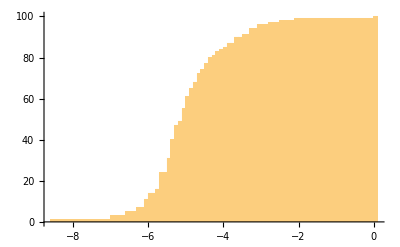

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-9.59583,0)(-8.59583,1)(-6.96352,2)(-6.96352,3)(-6.56445,4)(-6.56445,5)(-6.24408,6)(-6.24408,7)(-6.08923,8)(-6.05842,9)(-6.05842,10)(-6.01952,11)(-5.96053,12)(-5.90816,13)(-5.90816,14)(-5.78741,15)(-5.78741,16)(-5.66309,17)(-5.66309,18)(-5.65393,19)(-5.65393,20)(-5.64661,21)(-5.64661,22)(-5.62621,23)(-5.62621,24)(-5.49782,25)(-5.48292,26)(-5.48292,27)(-5.43695,28)(-5.43695,29)(-5.41572,30)(-5.41572,31)(-5.37965,32)(-5.37965,33)(-5.37259,34)(-5.37259,35)(-5.34788,36)(-5.34788,37)(-5.32995,38)(-5.32633,39)(-5.32633,40)(-5.26737,41)(-5.26737,42)(-5.24579,43)(-5.24579,44)(-5.22331,45)(-5.21373,46)(-5.21373,47)(-5.11148,48)(-5.11148,49)(-5.05318,50)(-5.05318,51)(-5.01638,52)(-5.01638,53)(-5.01055,54)(-5.01055,55)(-4.92985,56)(-4.92985,57)(-4.90371,58)(-4.90371,59)(-4.90095,60)(-4.90095,61)(-4.89587,62)(-4.89587,63)(-4.85788,64)(-4.85788,65)(-4.77724,66)(-4.72631,67)(-4.72631,68)(-4.67248,69)(-4.67248,70)(-4.67203,71)(-4.67203,72)(-4.5815,73)(-4.5815,74)(-4.48845,75)(-4.48845,76)(-4.43032,77)(-4.37087,78)(-4.36325,79)(-4.36325,80)(-4.21455,81)(-4.13112,82)(-4.13112,83)(-4.00825,84)(-3.9668,85)(-3.84514,86)(-3.84514,87)(-3.6397,88)(-3.60988,89)(-3.60988,90)(-3.45924,91)(-3.28126,92)(-3.22998,93)(-3.22998,94)(-3.09059,95)(-3.09059,96)(-2.77205,97)(-2.48276,98)(-2.0796,99)(0.,100)(0.5,100)

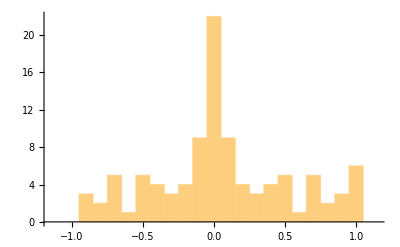

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.894764,1)(-0.867739,2)(-0.857723,3)(-0.833362,4)(-0.788403,5)(-0.744877,6)(-0.735218,7)(-0.703017,8)(-0.687684,9)(-0.677197,10)(-0.64892,11)(-0.549705,12)(-0.538618,13)(-0.538039,14)(-0.515539,15)(-0.505178,16)(-0.437622,17)(-0.393914,18)(-0.388708,19)(-0.374378,20)(-0.336264,21)(-0.325408,22)(-0.275426,23)(-0.243164,24)(-0.238317,25)(-0.225832,26)(-0.219427,27)(-0.146799,28)(-0.146043,29)(-0.138865,30)(-0.122112,31)(-0.112813,32)(-0.0964535,33)(-0.08557,34)(-0.0641624,35)(-0.0630675,36)(-0.0346658,37)(-0.0320883,38)(-0.0304751,39)(-0.0303555,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.0303555,55)(0.0304751,56)(0.0320883,57)(0.0346658,58)(0.0630675,59)(0.0641624,60)(0.08557,61)(0.0964535,62)(0.112813,63)(0.122112,64)(0.138865,65)(0.146043,66)(0.146799,67)(0.219427,68)(0.225832,69)(0.238317,70)(0.243164,71)(0.275426,72)(0.325408,73)(0.336264,74)(0.374378,75)(0.388708,76)(0.393914,77)(0.437622,78)(0.505178,79)(0.515539,80)(0.538039,81)(0.538618,82)(0.549705,83)(0.64892,84)(0.677197,85)(0.687684,86)(0.703017,87)(0.735218,88)(0.744877,89)(0.788403,90)(0.833362,91)(0.857723,92)(0.867739,93)(0.894764,94)(1.,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Data for topic patterns

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
Length[TopicClusters]
```

266

```mathematica
SelectedClusters=TopicClusters;
```

```mathematica
TopicClustersDutch=TopicClusters;
```

```mathematica
Timing[PnlTopic=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{225.781,Null}

```mathematica
Timing[PnlT=Table[v=Table[prepP=PnlTopic_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,100}];v/Total[v],{m,1,100}];]
```

{0.0625,Null}

```mathematica
Timing[spec=Eigenvalues[PnlT];]
```

{1.42188,Null}

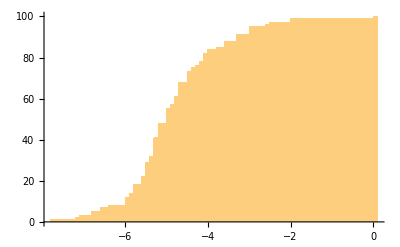

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-8.79771,0)(-7.79771,1)(-7.15093,2)(-7.09403,3)(-6.71694,4)(-6.71694,5)(-6.56042,6)(-6.56042,7)(-6.39587,8)(-5.97711,9)(-5.97711,10)(-5.92678,11)(-5.92678,12)(-5.88748,13)(-5.88748,14)(-5.7443,15)(-5.7443,16)(-5.72313,17)(-5.72313,18)(-5.59464,19)(-5.59464,20)(-5.54888,21)(-5.54888,22)(-5.49721,23)(-5.48982,24)(-5.48982,25)(-5.4571,26)(-5.4571,27)(-5.44005,28)(-5.44005,29)(-5.38967,30)(-5.34872,31)(-5.34872,32)(-5.29986,33)(-5.27772,34)(-5.27772,35)(-5.27242,36)(-5.27242,37)(-5.26381,38)(-5.26381,39)(-5.2505,40)(-5.2505,41)(-5.13581,42)(-5.13581,43)(-5.12453,44)(-5.12453,45)(-5.12146,46)(-5.12146,47)(-5.10202,48)(-4.98246,49)(-4.98246,50)(-4.97307,51)(-4.97307,52)(-4.93527,53)(-4.93527,54)(-4.92577,55)(-4.85902,56)(-4.85902,57)(-4.74799,58)(-4.74799,59)(-4.72508,60)(-4.72508,61)(-4.66798,62)(-4.66798,63)(-4.65854,64)(-4.65854,65)(-4.63889,66)(-4.63889,67)(-4.61429,68)(-4.48905,69)(-4.48905,70)(-4.41473,71)(-4.40424,72)(-4.40424,73)(-4.30989,74)(-4.30989,75)(-4.25094,76)(-4.10027,77)(-4.10027,78)(-4.05215,79)(-4.05215,80)(-4.00377,81)(-4.00377,82)(-3.98314,83)(-3.98314,84)(-3.79431,85)(-3.54328,86)(-3.51375,87)(-3.51375,88)(-3.28709,89)(-3.28709,90)(-3.24133,91)(-2.97324,92)(-2.97324,93)(-2.91809,94)(-2.91809,95)(-2.53706,96)(-2.40052,97)(-1.97651,98)(-1.92038,99)(0.,100)(0.5,100)

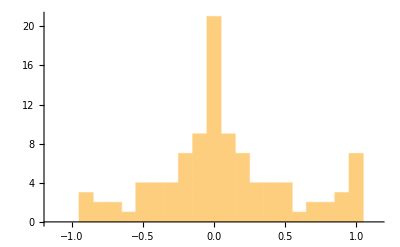

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.902768,1)(-0.868466,2)(-0.852594,3)(-0.81019,4)(-0.784464,5)(-0.70644,6)(-0.658076,7)(-0.552511,8)(-0.549594,9)(-0.531757,10)(-0.528726,11)(-0.522728,12)(-0.448496,13)(-0.383138,14)(-0.379072,15)(-0.378969,16)(-0.349451,17)(-0.344952,18)(-0.253333,19)(-0.250093,20)(-0.239024,21)(-0.227988,22)(-0.194744,23)(-0.187181,24)(-0.176073,25)(-0.152449,26)(-0.150004,27)(-0.13786,28)(-0.134629,29)(-0.119543,30)(-0.105945,31)(-0.0893086,32)(-0.0839277,33)(-0.0827359,34)(-0.0819975,35)(-0.0674763,36)(-0.0203945,37)(-0.0154211,38)(-0.0127739,39)(-0.0115583,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.0115583,54)(0.0127739,55)(0.0154211,56)(0.0203945,57)(0.0674763,58)(0.0819975,59)(0.0827359,60)(0.0839277,61)(0.0893086,62)(0.105945,63)(0.119543,64)(0.134629,65)(0.13786,66)(0.150004,67)(0.152449,68)(0.176073,69)(0.187181,70)(0.194744,71)(0.227988,72)(0.239024,73)(0.250093,74)(0.253333,75)(0.344952,76)(0.349451,77)(0.378969,78)(0.379072,79)(0.383138,80)(0.448496,81)(0.522728,82)(0.528726,83)(0.531757,84)(0.549594,85)(0.552511,86)(0.658076,87)(0.70644,88)(0.784464,89)(0.81019,90)(0.852594,91)(0.868466,92)(0.902768,93)(1.,94)(1.,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Word translation

#### Bulk vectors

```mathematica
EnglishRef=TopicClustersEnglish;
```

```mathematica
DutchRef=TopicClustersDutch;
```

```mathematica
PandPChapEnglish=StringSplit[ExampleData[{"Text","PrideAndPrejudice"}],"Chapter "~~DigitCharacter..~~" "];
```

```mathematica
Length[PandPChapEnglish]
```

61

```mathematica
VecEnglish=Table[{EnglishRef_⟦k,1⟧,StringCount[PandPChapEnglish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@EnglishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[EnglishRef]}];
```

```mathematica
PandPChapDutch=StringReplace[ImportString[#,"HTML"]&/@StringReplace[StringSplit[Import["Trots en vooroordeel.txt"],WordBoundary~~"Hoofdstuk"~~" "..~~DigitCharacter..~~WordBoundary],{"\n\n":>"垚"}],{"垚":>"\n\n"}];
```

```mathematica
Length[PandPChapDutch]
```

61

```mathematica
VecDutch=Table[{DutchRef_⟦k,1⟧,StringCount[PandPChapDutch,WordBoundary~~Alternatives@@(#_⟦1⟧&/@DutchRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[DutchRef]}];
```

```mathematica
FlatScreenedPairs=Flatten[Table[{#_⟦1⟧,#_⟦2,k⟧},{k,1,Length[#_⟦2⟧]}]&/@Select[Table[{EnglishRef[[k,1]],#_⟦1⟧&/@Select[VecDutch,JaccardRuzickaSim[#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧]≥Max[1-7/100*√61,1-√(Length[Select[Min[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}],#>0&]]/Total[Max[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}]])]&]},{k,1,Length[EnglishRef]}],Length[#_⟦2⟧]>0&],1];
```

```mathematica
SiftedTags=Union[(#_⟦1⟧&/@FlatScreenedPairs)];SiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SiftedTags=Union[(#_⟦2⟧&/@FlatScreenedPairs)];SiftedDutchRef=Reverse[SortBy[Table[Cases[DutchRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
Length[SiftedEnglishRef]
```

106

```mathematica
Length[SiftedDutchRef]
```

106

#### Spectral parameters for English

```mathematica
FromTopics=SiftedEnglishRef;
```

```mathematica
FromDelta=ReadDelta[#]&/@FromTopics;
```

```mathematica
FromN=(#_⟦3⟧-1)&/@FromTopics;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersEnglish,PenTopic,#_⟦1⟧&/@FromTopics];]
```

{57.4652,Null}

```mathematica
FromKinQ=KinQ;
```

```mathematica
FromEta=SemanticComplexities;
```

#### Spectral parameters for Dutch

```mathematica
ToTopicsDutch=SiftedDutchRef;
```

```mathematica
Length[ToTopicsDutch]
```

106

```mathematica
ToDeltaDutch=ReadDelta[#]&/@ToTopicsDutch;
```

```mathematica
ToNDutch=(#_⟦3⟧-1)&/@ToTopicsDutch;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersDutch,PnlTopic,#_⟦1⟧&/@ToTopicsDutch];]
```

{80.8484,Null}

```mathematica
ToKinDutch=KinQ;
```

```mathematica
ToEtaDutch=SemanticComplexities;
```

#### Translation

```mathematica
AbsoluteTiming[fromLabeled=Transpose[{#_⟦1⟧&/@FromTopics,FromKinQ}];toLabeled=Transpose[{#_⟦1⟧&/@ToTopicsDutch,ToKinDutch}];Report=Table[{FlatScreenedPairs_⟦k⟧,(JaccardRuzickaSim[Cases[fromLabeled,{FlatScreenedPairs_⟦k,1⟧,_}]_⟦1,2⟧,Cases[toLabeled,{FlatScreenedPairs_⟦k,2⟧,_}]_⟦1,2⟧])},{k,1,Length[FlatScreenedPairs]}];]
```

{0.015399,Null}

```mathematica
prep=Union[Select[Table[{Report_⟦n,1,1⟧,Report_⟦n,1,2⟧,Report_⟦n,2⟧},{n,1,Length[Report]}],#_⟦3⟧≥0.7&]];g=Graph[(#_⟦1⟧->#_⟦2⟧)&/@prep,EdgeWeight->(#_⟦3⟧&/@prep)];(KuhnSln={#,FindRowRank[#,prep],FindColRank[#,prep]}&/@Select[{#,PropertyValue[{g,#},EdgeWeight]}&/@FindIndependentEdgeSet[g],#_⟦2⟧>0&])//TableForm
```

{{Brighton,24}}->{{brighton,24}}
0.91468664742001 | 1 | 1
{{de,39}}->{{bourgh,38}}
0.91806176844139 | 1 | 1
{{Derbyshire,24}}->{{derbyshire,28}}
0.85072308553558 | 1 | 1
{{five,30}}->{{vijfduizend,4},{vijfentwintig,2},{vijfenveertig,1},{vijftien,6},{vijf,30},{vijfde,1}}
0.90479616204429 | 1 | 1
{{library,23}}->{{bibliotheek,21},{familiebibliotheek,1}}
0.94284293170844 | 1 | 1
{{London,55}}->{{londen,115}}
0.78770421017182 | 1 | 1
{{Mr,786}}->{{mijnheer,799}}
0.82730345566634 | 1 | 1
{{Mrs,343}}->{{mevrouw,370}}
0.91292402591889 | 1 | 1
{{Netherfield,73}}->{{netherfield,76}}
0.85213818826415 | 1 | 1
{{oh,95}}->{{o,88}}
0.92826609678142 | 1 | 1
{{park,22}}->{{park,26}}
0.83003695742217 | 1 | 1
{{Pemberley,53}}->{{pemberley,56}}
0.83908749548957 | 1 | 1
{{pounds,24}}->{{pond,36}}
0.8911872577166 | 1 | 1
{{thousand,34}}->{{dertigduizend,1},{drieduizend,2},{tienduizend,11},{twintigduizend,1},{vierduizend,2},{vijfduizend,4},{vijftigduizend,1},{zesduizend,1},{duizend,8},{duizenden,1},{duistere,1}}
0.76536381466354 | 2 | 2
{{Rosings,49}}->{{rosings,49}}
0.94576969344575 | 1 | 1
{{sir,78}}->{{william,44},{williams,3}}
0.90773300288509 | 1 | 1
{{William,40},{William's,6}}->{{sir,48}}
0.90385350550291 | 1 | 2
{{two,135}}->{{twee,148}}
0.88900567667158 | 1 | 2
{{absence,27},{absent,4}}->{{afwezig,8},{afwezigheid,22}}
0.7838852720789 | 1 | 1
{{ball,34},{balls,8}}->{{balschoentjes,1},{balzaal,2},{bal,43},{bals,11}}
0.89860146007252 | 1 | 1
{{Catherine,110},{Catherine's,16}}->{{lady,169}}
0.92012124425798 | 1 | 1
{{Charlotte,68},{Charlotte's,17}}->{{charlotte,87},{charlottes,3}}
0.92890331594115 | 1 | 1
{{Collins,156},{Collins's,24}}->{{collins,186},{collinsen,2}}
0.93874228183118 | 1 | 1
{{colonel,65},{colonel's,1}}->{{kolonel,67}}
0.84358180763438 | 1 | 1
{{Darcy,374},{Darcy's,44}}->{{darcy,421}}
0.93413372975662 | 1 | 1
{{dinner,33},{dinners,2}}->{{familiediner,2},{diner,25},{diners,2},{dineren,27}}
0.91293890472792 | 1 | 1
{{elegance,9},{elegant,14}}->{{elegantie,4},{elegant,3},{elegante,12},{eleganter,1},{elegantere,1}}
0.75746923416098 | 1 | 1
{{father,116},{father's,19}}->{{vader,129},{vaders,11}}
0.89747565412603 | 1 | 1
{{Fitzwilliam,32},{Fitzwilliam's,5}}->{{fitzwilliam,37}}
0.79552348054704 | 1 | 1
{{four,33},{four-and-twenty,1}}->{{vier,28},{vierduizend,2},{vierentwintig,1},{vierhonderd,1},{viermaal,5},{viertal,1}}
0.89737930594424 | 1 | 1
{{girl,38},{girls,45}}->{{meisje,32},{meisjes,53}}
0.91491704965354 | 1 | 1
{{glad,37},{gladly,1}}->{{blij,34},{blijmoedig,1}}
0.73645693770744 | 1 | 1
{{Jane,263},{Jane's,28}}->{{jane,304}}
0.84359498206107 | 1 | 1
{{Kitty,69},{Kitty's,2}}->{{kitty,71}}
0.95142862422231 | 1 | 1
{{Lizzy,95},{Lizzy's,2}}->{{lizzy,94}}
0.96024053924633 | 1 | 1
{{Lydia,133},{Lydia's,38}}->{{lydia,172}}
0.88854270213835 | 1 | 1
{{Mary,38},{Mary's,1}}->{{mary,41}}
0.89953907023277 | 1 | 1
{{people,46},{people's,4}}->{{mensen,65},{menselijk,1},{menselijke,6},{menselijkheid,1},{mensheid,1}}
0.91231223009447 | 1 | 1
{{poor,38},{poorly,3}}->{{alarmerende,1},{armbanden,1},{armlastig,1},{arm,7},{arme,25},{armen,4}}
0.82009598277693 | 1 | 1
{{regiment,19},{regiment's,3}}->{{regende,1},{regenen,4},{regiment,25}}
0.91166920910409 | 1 | 1
{{room,112},{rooms,8}}->{{boekenkamer,1},{kamermeisje,2},{slaapkamer,1},{slaapkamers,1},{kamenier,1},{kamer,94},{kamers,8}}
0.85335731944521 | 1 | 1
{{serious,24},{seriously,13}}->{{serieus,23},{serieuze,6},{serieuzer,1},{serieuzere,2}}
0.81522650315639 | 1 | 1
{{table,28},{tables,3}}->{{lanterluitafel,1},{schrijftafel,1},{tafel,31},{tafels,2},{tafeltje,1}}
0.87736182145785 | 1 | 1
{{ten,33},{tens,1}}->{{tienduizend,11},{tienmaal,1},{tientallen,2},{veertien,3},{vijftien,6},{tien,18},{tienden,1},{zestien,7},{zestiende,1}}
0.75457371600292 | 1 | 1
{{week,29},{weeks,18}}->{{week,33},{weken,36},{wijken,4},{afwijken,1}}
0.79758173479583 | 1 | 1
{{Wickham,162},{Wickham's,32}}->{{wickham,182},{wickhams,12}}
0.853248920013 | 1 | 1
{{window,16},{windows,6}}->{{raamlijst,1},{raam,14},{ramen,4},{room,2},{ruim,2}}
0.80074345262323 | 1 | 1
{{aunt,78},{aunt's,6},{aunts,1}}->{{tante,89},{tantes,1}}
0.91712818616763 | 1 | 1
{{Bennet,294},{Bennet's,29},{Bennets,10}}->{{bennet,316},{bennets,5}}
0.8987427903048 | 1 | 1
{{book,16},{books,13},{book-room,1}}->{{boekenkamer,1},{muziekboeken,1},{boek,20},{boeken,15}}
0.81711762943086 | 1 | 1
{{child,14},{children,25},{childhood,1}}->{{kind,17},{kinderen,29},{kindertijd,2}}
0.90355769001577 | 1 | 1
{{cried,91},{cry,1},{crying,2}}->{{afriep,1},{opriep,2},{riep,103},{riepen,2}}
0.7977601675793 | 1 | 1
{{dear,158},{dearly,3},{dearest,17}}->{{liefhebben,1},{liefhebbend,2},{liefhebbende,7},{lief,9},{liefst,4},{liefste,12},{lieve,117},{lieveling,2},{lievelingen,2},{liever,18},{liefde,39},{liefdevol,1},{liefdevolle,2}}
0.83502531815918 | 1 | 1
{{Eliza,22},{Elizabeth,597},{Elizabeth's,38}}->{{elizabeth,636},{elizabeths,15}}
0.85900902722981 | 1 | 1
{{evening,72},{evening's,2},{evenings,4}}->{{avond,71},{avonds,11},{avonden,4},{avondeten,2}}
0.86672243318804 | 1 | 1
{{eye,15},{eyeing,1},{eyes,52}}->{{oogmerk,1},{oogwenk,2},{ogen,56},{oog,9}}
0.80984440017695 | 1 | 1
{{Forster,38},{Forster's,1},{Forsters,1}}->{{forster,39},{forsters,1}}
0.90399268914553 | 1 | 1
{{Gardiner,84},{Gardiner's,13},{Gardiners,6}}->{{gardiner,95},{gardiners,5}}
0.91322777607022 | 1 | 1
{{hand,24},{handed,3},{hands,7}}->{{handgebaar,1},{handschoen,2},{handtas,1},{hand,46},{handen,2},{handwerk,3},{handwerken,1}}
0.77238843143958 | 1 | 1
{{letter,115},{letters,16},{letter-paper,1}}->{{briefpapier,1},{briefwisseling,2},{zakenbrieven,1},{brief,137},{brieven,17},{briefje,8},{briefjes,1}}
0.70969558486849 | 1 | 1
{{man,145},{man's,5},{men,33}}->{{man,131},{mannen,16}}
0.87688213040482 | 1 | 1
{{maternal,2},{mother,110},{mother's,25}}->{{moelijk,1},{moe,5},{moed,13},{mama,9},{mamma,2},{moeder,135},{moeders,6}}
0.89897661817433 | 1 | 1
{{Phillip's,1},{Phillips,26},{Phillips's,5}}->{{philips,36}}
0.88356239344598 | 1 | 1
{{read,40},{reading,14},{reader,3}}->{{gelezen,5},{las,22},{lees,2},{lezen,20},{leest,3}}
0.8443319690001 | 1 | 1
{{sore,1},{sorely,1},{sorry,34}}->{{respijt,1},{spijt,33},{spijten,4}}
0.84643423449416 | 1 | 1
{{uncle,59},{uncle's,9},{uncles,3}}->{{oom,71},{ooms,3}}
0.92304850707092 | 1 | 1
{{year,28},{years,33},{years',2}}->{{halfjaar,1},{jaarlijks,2},{jeugdjaren,1},{jaar,61},{jaren,15}}
0.76839452607229 | 1 | 1
{{young,130},{younger,30},{youngest,13}}->{{jongedame,14},{jongedames,30},{jongedames,1},{tjongejonge,1},{jong,9},{jonge,29},{jongen,3},{jongens,3},{jongetjes,1},{jonger,5},{jongere,20}}
0.84898097271132 | 1 | 1
{{Bingley,257},{Bingley's,49},{Bingleys,4},{Bingleys',1}}->{{bingley,306},{bingleys,10}}
0.8888008290693 | 1 | 1
{{brother,62},{brotherly,2},{brother's,13},{brothers,2}}->{{broer,66},{broers,1},{broertjes,1}}
0.86989133396702 | 1 | 1
{{character,64},{characters,3},{characteristic,2},{characterise,1}}->{{karakter,71},{karakters,7}}
0.8550031544483 | 1 | 1
{{complied,4},{compliment,26},{compliments,11},{compliance,1}}->{{complimentjes,2},{compliment,19},{complimenten,11},{complimenteer,1},{complimenteren,1},{complimenteert,1},{complimenteerde,3}}
0.74226885570696 | 1 | 1
{{daily,3},{day,130},{day's,4},{days,30}}->{{dagelijks,1},{daglicht,2},{dagtekening,1},{huwelijksdag,1},{trouwdag,1},{vrijdag,1},{zondag,7},{dag,123},{daag,1},{dagen,38},{opdagen,1},{gedoogt,1},{mededogen,1}}
0.84579652260259 | 2 | 1
{{dance,31},{danced,12},{dances,10},{dancing,21}}->{{danskunst,3},{dansparen,3},{danspartner,1},{dansvloer,3},{dansen,44},{danst,5},{danste,5},{dansten,2},{gedanst,8}}
0.7828775113963 | 1 | 1
{{daughter,78},{daughter's,7},{daughters,49},{daughters',1}}->{{dochter,88},{dochters,56}}
0.91588040176534 | 1 | 1
{{handsome,37},{handsomely,2},{handsomer,3},{handsomest,4}}->{{knap,35},{knappe,9},{knapper,3},{opgeknapt,3}}
0.89776659993359 | 1 | 1
{{honour,42},{honoured,9},{honours,2},{honourable,6}}->{{eer,36},{ere,2}}
0.85024696284772 | 1 | 1
{{Lucas,65},{Lucas's,5},{Lucases,13},{Lucases',1}}->{{lucas,81},{lucassen,1}}
0.92986512485999 | 1 | 1
{{said,401},{say,160},{saying,35},{says,15}}->{{gezeglijke,1},{opzeggen,1},{toegezegd,3},{gezegd,50},{zeg,40},{zeggen,157},{zei,374},{zeiden,8},{zegt,24}}
0.89408595253668 | 1 | 1
{{seem,16},{seemed,66},{seeming,3},{seems,22}}->{{laakbaar,4},{laks,1},{lake,5},{leek,67},{leken,9}}
0.75611074676777 | 1 | 1
{{tell,71},{telling,7},{tells,1},{told,69}}->{{vertel,12},{vertellen,58},{verteld,37},{vertelde,46},{vertelden,1},{vertelt,3},{doorvertelde,1}}
0.77382003048958 | 1 | 1
{{believed,37},{believing,12},{belief,15},{believe,87},{believes,1}}->{{geloof,44},{geloven,51},{geloofd,3},{geloofde,20},{gelooft,6}}
0.88352143876527 | 1 | 1
{{carriage,44},{carriages,6},{carried,8},{carry,5},{carrying,4}}->{{rijtuig,48},{rijtuigen,6}}
0.82428640124263 | 1 | 1
{{console,9},{consoled,2},{consoling,3},{consolation,10},{consolatory,1}}->{{getroost,1},{getroosten,1},{troost,26},{troostvolle,1},{troosten,7},{getroostte,1},{troostten,1}}
0.86306283722501 | 1 | 1
{{happily,5},{happiness,72},{happy,83},{happier,3},{happiest,10}}->{{gelukwensen,10},{geluk,84},{gelukkig,71},{gelukkige,15},{gelukt,1},{lukken,2},{lukt,1}}
0.85574395184653 | 1 | 1
{{house,106},{houses,4},{household,1},{housemaid,2},{housemaids,1}}->{{huisgenoten,2},{huishouden,5},{huishouding,3},{huisknecht,1},{pakhuizen,1},{huiselijk,5},{huiselijke,3},{huis,126},{huize,1},{huizen,3},{huizes,8}}
0.87014552005439 | 1 | 1
{{invite,6},{invited,11},{inviting,3},{invitation,34},{invitations,1}}->{{uitnodigen,4},{uitnodiging,29},{uitnodigingen,2},{uitnodigde,2}}
0.88547923176154 | 1 | 1
{{knew,58},{know,238},{knowing,27},{known,57},{knows,9}}->{{afweten,1},{geweten,14},{weet,154},{weten,120},{wetens,1},{wist,97},{wisten,10},{wijten,3}}
0.95039669534111 | 1 | 1
{{laugh,18},{laughed,11},{laughing,10},{laughingly,2},{laughter,2}}->{{lachwekkend,2},{gelach,1},{gelachen,5},{lach,15},{lachen,29},{lachend,2},{lachte,14},{lachten,3},{toegelachen,1}}
0.90352160946007 | 1 | 1
{{length,32},{long,114},{longed,9},{longing,2},{longer,44}}->{{langdurig,2},{langsreed,1},{tijdlang,1},{lang,120},{langs,28},{lange,22},{langer,31},{langere,1}}
0.82416745258268 | 1 | 1
{{miss,283},{missed,3},{missing,1},{missent,2},{missish,1}}->{{juffrouw,252}}
0.90203773522891 | 1 | 1
{{pride,47},{prided,1},{proud,22},{proudly,1},{proudest,1}}->{{trots,47}}
0.91403700640098 | 1 | 1
{{saw,103},{see,149},{seeing,60},{seen,76},{sees,6}}->{{aanzienlijker,1},{eruitzag,3},{afgezien,6},{aangezien,58},{aanzien,13},{aanzienlijk,4},{aanzienlijke,4},{doorzien,1},{gezien,89},{opzag,1},{opzicht,7},{opzichte,2},{opzichten,9},{opzichtig,1},{opzichtige,1},{toezicht,5},{toeziend,1},{zag,114},{zagen,13},{zicht,11},{zien,152},{ziens,1},{zichtbaar,7}}
0.78560644980679 | 1 | 1
{{serve,2},{serving,1},{servant,15},{servant's,2},{servants,12}}->{{bedienend,1},{bediende,15},{bedienden,12}}
0.85343545779438 | 1 | 1
{{woman,55},{womanly,1},{woman's,4},{women,19},{women's,1}}->{{buurvrouw,6},{officiersvrouwen,1},{vrouw,110},{vrouwen,21},{vrouwelijk,1},{vrouwelijke,3}}
0.7771487776235 | 1 | 1
{{feel,39},{feeling,38},{feelingly,1},{feelings,86},{feels,4},{felt,100}}->{{diepgevoelde,1},{schuldgevoelens,1},{aanvoelde,1},{voelde,54},{voelden,5},{gevoel,50},{gevoeld,15},{gevoelen,4},{gevoelens,148},{gevoeligheid,2},{meevoelen,2},{voel,9},{voelen,22},{voelt,10}}
0.89428738882253 | 1 | 1
{{office,6},{officer,8},{officers,29},{officers',2},{officiousness,1},{officious,3}}->{{officieren,30},{officierspost,1},{officiersvrouwen,1}}
0.81880635615433 | 1 | 1
{{visit,51},{visited,4},{visiting,5},{visits,5},{visitor,11},{visitors,14}}->{{bezocht,4},{bezoek,78},{bezoeken,12},{bezoeker,5},{bezoekers,7},{bezoeking,1},{bezoekje,1},{bezoekjes,2},{bezoekster,1}}
0.86445480580863 | 1 | 1
{{write,39},{writes,1},{writing,12},{written,19},{writer,3},{wrote,21}}->{{volgeschreven,2},{geschreven,20},{omschreven,1},{omschrijven,1},{omschrijving,2},{schreef,19},{schrijf,11},{schrijven,40},{toegeschreven,4},{toeschreef,1},{toeschrijf,1},{toeschrijven,3}}
0.85620019235487 | 1 | 1
{{speak,66},{speaking,33},{speaks,3},{speaker,1},{spoke,43},{spoken,16},{spokesman,1}}->{{spraakzaam,2},{vrijsprak,1},{vrijspreken,1},{afspraak,8},{afspraken,6},{aansprak,2},{aanspraak,7},{aanspraken,3},{aanspreken,1},{opspraak,1},{sprak,74},{spraak,1},{sprake,17},{spraken,17},{spreek,8},{spreken,81},{sprekend,2},{toesprak,1},{toespraak,2}}
0.87557671289658 | 1 | 1
{{gentle,5},{gentleness,4},{gentlemen,34},{gentlemen's,3},{gentleman,32},{gentleman's,8},{gentlemanlike,8},{gentlest,1},{gentlewoman,1}}->{{heer,52},{heren,43},{heerlijk,7},{heerlijke,1},{heerlijkheid,1},{heerlijkste,1}}
0.87116428087533 | 1 | 1

```mathematica
ResiftedTags=Union[(#_⟦1⟧&/@prep)];ResiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
ResiftedTags=Union[(#_⟦2⟧&/@prep)];ResiftedDutchRef=Reverse[SortBy[Table[Cases[DutchRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SemanticSim={Position[ResiftedEnglishRef,{#_⟦1⟧,___}]_⟦1,1⟧,Position[ResiftedDutchRef,{#_⟦2⟧,___}]_⟦1,1⟧,#_⟦3⟧}&/@prep;
```

```mathematica
OptimalNodes={Position[ResiftedEnglishRef,{#_⟦1,1,1⟧,___}]_⟦1,1⟧,Position[ResiftedDutchRef,{#_⟦1,1,2⟧,___}]_⟦1,1⟧,#_⟦2,1,1⟧,#_⟦3,1,1⟧}&/@KuhnSln;
```

```mathematica
Export["PnP_EnglishDutch.txt","%tournament\n"<>StringJoin[Riffle[Flatten["\\put("<>ToString[1.5+1+4#_⟦2⟧]<>","<>ToString[90-4#_⟦1⟧]<>"){\\color[rgb]"<>ToString[TempRGB[#_⟦3⟧]]<>"{\\rule{4pt}{4pt}}}"&/@SemanticSim],"\n"]]<>"\n%crosshairs\n"<>StringJoin[Riffle["\n%"<>ResiftedEnglishRef[[#_⟦1⟧,1,1,1]]<>"_"<>ResiftedDutchRef[[#_⟦2⟧,1,1,1]]<>"
\\put("<>ToString[1.5+4#_⟦2⟧+3]<>","<>ToString[90-4#_⟦1⟧+2]<>"){\\color{green}\\linethickness{"<>ToString[1.5/#_⟦3⟧]<>"pt}\\line(-1,0){"<>ToString[4#_⟦2⟧-2]<>"}\\linethickness{"<>ToString[1.5/#_⟦4⟧]<>"pt}\\line(0,1){"<>ToString[4#_⟦1⟧-2]<>"}}"&/@OptimalNodes,"\n"]]];
```

#### English labels

```mathematica
FromClusters=ResiftedEnglishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["EnglishLabels_for_Dutch_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5-3Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[91.75-1.5-4k]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

#### Dutch labels

```mathematica
FromClusters=ResiftedDutchRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
DutchSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@AlphabeticSort[Keys[assoc],"Dutch"])]
```

```mathematica
AdmissibleDutchVerbPrefixes=""|"af"|"aan"|"door"|"dwars"|"bij"|"mee"|"mede"|"na"|"om"|"op"|"voort"|"her"|"be"|"ver"|"mede"|"na"~~""|"ge";
```

```mathematica
DutchDoublets=Alternatives@@(#<>#&/@CharacterRange["a","z"])
```

aa|bb|cc|dd|ee|ff|gg|hh|ii|jj|kk|ll|mm|nn|oo|pp|qq|rr|ss|tt|uu|vv|ww|xx|yy|zz

```mathematica
RemoveExtraSpace[cl_]:=(sp=Max[0,Min[First[#]_⟦1⟧&/@StringPosition[Transpose[cl]_⟦1⟧,Except[" "],1]-1]];Table[{StringDrop[cl_⟦n,1⟧,sp],cl_⟦n,2⟧},{n,1,Length[cl]}])
```

```mathematica
DutchCompress[w_]:=(Lprot=Max[0,Max[Flatten[StringLength/@StringCases[w," "..]]]];StringTake[#,UpTo[Lprot]]<>StringReplace[StringDrop[#,UpTo[Lprot]],{(x:DutchDoublets):>ToUpperCase[StringTake[x,1]],"ie":>"𝕀","ei":>"𝔼","ij":>"𝕐","ui":>"𝕌","oe":>"𝕆"}]&/@w)
```

```mathematica
DutchDecompress[w_]:=StringReplace[w,{X:Alternatives@@CharacterRange["A","Z"]:>ToLowerCase[X]<>ToLowerCase[X],"𝕀":>"ie","𝔼":>"ei","𝕐":>"ij","𝕌":>"ui","𝕆":>"oe"}]
```

```mathematica
PadPrefix0[cl_]:=(HeuristicPrefixL=(Max[#]-1)&/@((Last[#]&/@StringPosition[#,WordBoundary~~AdmissibleDutchVerbPrefixes~~WordCharacter,Overlaps->All])&/@cl_⟦1⟧);MaxPrefixL=Max[HeuristicPrefixL];{Table[{StringDrop[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],StringPadLeft[StringTake[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],MaxPrefixL," "]},{n,1,Length[cl_⟦1⟧]}],cl_⟦2⟧})
```

```mathematica
PadPrefix[cl_]:=DutchSort[RefString=RemoveDiacritics[Last[SortBy[#_⟦1⟧&/@cl_⟦1⟧,StringLength[#]&]],Language->"Dutch"];Transpose[Table[prep=SequenceAlignment[RefString,RemoveDiacritics[cl_⟦1,n,1⟧,Language->"Dutch"]];If[Length[prep_⟦1⟧]>1,Lmax=Max[StringLength/@prep_⟦1⟧];{Table[" ",{m,1,Lmax-StringLength[prep_⟦1,2⟧]}]<>cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧},{cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧}],{n,1,Length[cl_⟦1⟧]}]]]
```

```mathematica
ClusterCount={{"aankomen","komen","aangekomen"},{10,72,83}}
```

{{aankomen,komen,aangekomen},{10,72,83}}

```mathematica
EvenOut[cl_]:=(prep0=PadPrefix[PadPrefix0[cl]];prep=DutchCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];RemoveExtraSpace[{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}]])
```

```mathematica
EvenOut[ClusterCount]
```

{{     komen,72},{  aankomen,10},{aangekomen,83}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,DutchDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
 
72 | 2
 
72 | 3
 
72 | 4
 
72 | 5
 
72 | 6
k
72 | 7
o
72 | 8
m
72 | 9
e
72 | 10
n
72
1
 
10 | 2
 
10 | 3
a
10 | 4
a
10 | 5
n
10 | 6
k
10 | 7
o
10 | 8
m
10 | 9
e
10 | 10
n
10
1
a
83 | 2
a
83 | 3
n
83 | 4
g
83 | 5
e
83 | 6
k
83 | 7
o
83 | 8
m
83 | 9
e
83 | 10
n
83

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{10,n,72},{10,n,10},{10,n,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
 
72 | 1
 
10 | 1
a
83
2
 
72 | 2
 
10 | 2
a
83
3
 
72 | 3
a
10 | 3
n
83
4
 
72 | 4
a
10 | 4
g
83
5
 
72 | 5
n
10 | 5
e
83
6
komen
165 |  |

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
a
83 | 1
 
82 | 
2
a
83 | 2
 
82 | 
3
n
83 | 3
a
10 | 3
 
72
4
g
83 | 4
a
10 | 4
 
72
5
e
83 | 5
n
10 | 5
 
72
6
komen
165 |  |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{6},komen,165,0}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["DutchLabels_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5.25-.25+1+4k]<>","<>ToString[91]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BCR{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C"}];RemoveDiacritics[temp1,Language->"English"]==temp1,1,1.3],10^-3]]])<>"}{"<>(If[StringDelete[temp,CharacterRange["A","Z"]]=="",temp,StringReplace[StringReplace[StringReplace[ExportString[temp,"TeX"],"\\ss":>"{\\ss}"],___~~"\\[\\text{":>""],"}\\]"~~___:>""]])<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

```mathematica
Export["EnglishDutch_Report.txt",{Last[SortBy[#_⟦1,1,1⟧,Last]]_⟦1⟧,Last[SortBy[#_⟦1,1,2⟧,Last]]_⟦1⟧}&/@KuhnSln];
```